```mathematica
genSound[ music_]:=(
soundNoteList[list_]:= Apply[SoundNote, list];
generated = Map[soundNoteList, music];
sound = Sound[generated];
Return[sound];
)
```

```mathematica
ApplyAndJoin[fn_, count_]:=(
Flatten[Map[fn, Range[count]]]
)
```

```mathematica
(* Přečtěte si dokumentaci na https://reference.wolfram.com/language/ref/SoundNote.html *)
```

```mathematica
music = {{{0,-10}, "Piano"}}
genSound[music]
```

```mathematica
genSound[{{{0,4}, "Harpsichord"}}]
```

```mathematica
{{genSound[{{2, "Harpsichord"}}]}, {□}}
```

```mathematica
{{Sound}, {□}}[{SoundNote[{0,4},{0,2},"Hapsichord"]}]
```

```mathematica
{{genSound[{{2, "Harpsichord"}}]}, {□}}
```

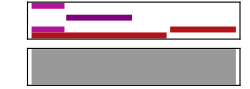

{{{0,4},{0,0.5},Harpsichord},{2,{0.5,1.5},Piano},{-1,2,Flute},{0,1,Flute}}

-Graphics-

{{{0,4},{0,0.5},Harpsichord},{2,{0.5,1.5},Piano},{-1,2,Flute},{0,1,Flute}}

-Graphics-

{{{0,4},{0,0.5},Harpsichord},{2,{0.5,1.5},Piano},{-1,2,Flute},{0,1,Flute}}

-Graphics-

```mathematica
music = {{{0,4}, {0,0.5}, "Harpsichord"},{2, {0.5,1.5}, "Piano"}, {-1, 2, "Flute" }, {0,1,"Flute"}}
genSound[music]
```

```mathematica
music = {{{0,4}, "Harpsichord"}}
genSound[music]
```

```mathematica
NormalDistribution[0,1]
```

```mathematica
RandomVariate[NormalDistribution[0.5, 0.5]]
ChooseTone[previous_,weights_,toneWeights_, toneImportance_]:=(
allTones=Range[-Length[weights],Length[weights]]+previous;
allIntervalWeights=Join[Reverse[Drop[weights,-1]],weights];
allToneWeights=Map[Function[t,Part[toneWeights,t % Length[toneWeights]]],allTones];
tone = RandomSample[(allToneWeights * allIntervalWeights) ^ toneImportance -> allTones)
)
```

```mathematica
GetMelody[size_, weights_, toneWeights_] := (
melody = {0};
For[i=1, i<size,i++, (
previous = Part[melody, i];
interval = RandomSample[weights->{0, 1, 2,3, 4, 5, 6, 7, 8}, 1];
interval = If[RandomReal[]>0.5, interval, -interval];
next = interval+ previous;
AppendTo[melody, next];
)];
Return[melody];
)
```

```mathematica
CreateMusic[melody_, tones_, rythm_] := (
music = {};
For[i=0, i<Length[melody],i++, (
toneOffset = Part[melody, i+1];
tone = Part[tones, 1 + Mod[toneOffset, Length[tones]]] + (Floor[toneOffset / Length[tones]] * 12);
sound = {tone, Part[rythm, i + 1] * 1.5, "Piano"};
AppendTo[music,sound];
)];
Return[music];
)
```

```mathematica
GetTact[divCoef_, recursionCoef_] := (
If[RandomReal[] > divCoef,(
Return[{1}]
),(
divLen[e_] := e / 2;
Return[ Map[divLen, Join[GetTact[divCoef / recursionCoef, recursionCoef], GetTact[divCoef/recursionCoef, recursionCoef]]]];
)]
)
```

```mathematica
GetRythm[divCoef_, recursionCoef_, size_] := 
ApplyAndJoin[Function[i, GetTact[divCoef, recursionCoef]], size]
```

{0,{-8},{-15},{-11},{-14},{-20},0,{4},{10},0,{4},{5},{9},{6},{8},0,{4},{10}}

{0,{-2},{0},{3},{6},{8},{10},0,{0},{1},0,{-2},{-6},{-5},{-4},{-7},{-5},0,{0},{1}}

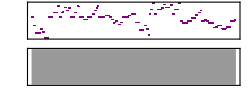

```mathematica
rtm1 = GetRythm[2.3, 3,  1];
rtm2 = GetRythm[2.3, 3,  1];
tones = {0, 2, 3, 5, 7, 8, 10} + 0;
weights = {1, 3, 5, 4, 4, 0.7,0.7, 1.2, 1};
mainM = GetMelody[Length[rtm]];
melody1 = Join[GetMelody[Length[rtm1], weights], ReplacePart[mainM, Length[rtm2]-> 4], GetMelody[Length[rtm1], weights], ReplacePart[mainM, Length[rtm2]->0]]
mainM = GetMelody[Length[rtm]];
melody2 = Join[GetMelody[Length[rtm2], weights], ReplacePart[mainM, Length[rtm1]-> 4], GetMelody[Length[rtm2], weights], ReplacePart[mainM, Length[rtm1]->0]]

genSound[CreateMusic[Join[melody1, melody2, melody1+3, melody2-4],tones,ApplyAndJoin[Function[i, Join[rtm1, rtm2, rtm1, rtm2, rtm2, rtm1, rtm2, rtm1]], 2]]]
```

```mathematica
ConstantArray[1/4, 8]
```

```mathematica
NumberForm[0.7611540449832752,100]
```

{1/2,{1/4,{1/4}}}

{1/2,{1/4,{1/4}}}

{1/2,{1/4,{1/4}}}

«16 more identical outputs»

{1/4,{1/4},{1/2}}

{1/2,{1/4,{1/4}}}

{1/4,{1/4},{1/2}}

GetRythm[1,2]

GetRythm[1,2]

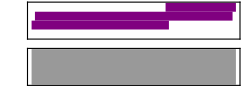

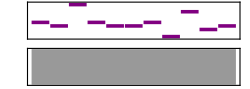
6 -Graphics-

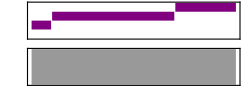

```mathematica
{1/2,{1/4,{1/4}}}
```

```mathematica
ApplyAndJoin[Function[i,{ RandomReal[], i}], 10]
```